```mathematica
DATAPATH = "C:\\Users\\pullin\\Desktop\\GIT code\\roach\\python\\Data";
```

```mathematica
(*DATAPATH="C:\\Users\\pullin\\Desktop\\GIT code\\pydebug"*)
```

```mathematica
DATAFILE="2015.01.08_15.41.38_trial_imudata.txt";
SetDirectory[DATAPATH];
(*SetDirectory["C:\\Users\\pullin\\Desktop\\SVN code\\trunk\\octoroach\\python"];*)
data = Import[DATAFILE,"CSV","HeaderLines"->11];
count2deg =1/ 14.375; 
Dimensions[data]
times = data[[All,1]]/10^6;
RlegPos= data[[All,2]]/65535;
LlegPos= data[[All,3]]/65535;
CmdRlegPos= data[[All,4]]/65535;
CmdLlegPos= data[[All,5]]/65535;
DCR= data[[All,6]];
DCL= data[[All,7]];
GyroX= data[[All,8]]*count2deg;
GyroY= data[[All,9]]*count2deg;
GyroZ= data[[All,10]]*count2deg;
AccelX= data[[All,11]];
AccelY= data[[All,12]];
AccelZ= data[[All,13]];
RBEMF= data[[All,14]];
LBEMF= data[[All,15]];
Vbatt= data[[All,16]];
```

{2198,16}

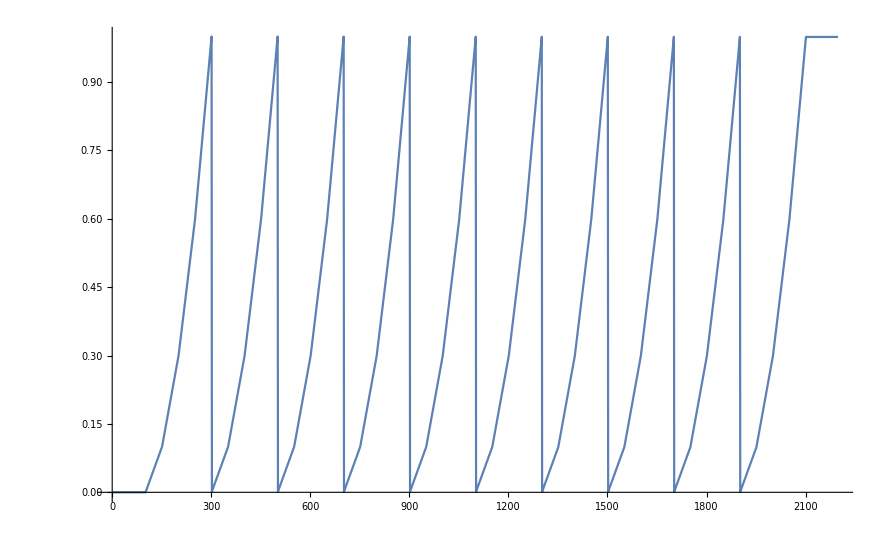

```mathematica
ListPlot[Mod[CmdRlegPos-CmdRlegPos[[1]],1],Joined->True]
```

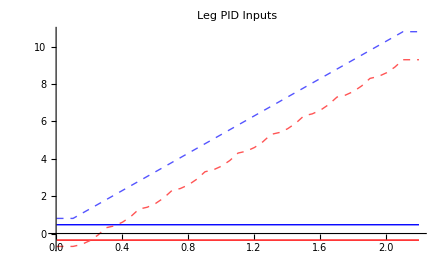

```mathematica
ListPlot[{{times,RlegPos}ᵀ,{times,LlegPos}ᵀ,{times,CmdRlegPos}ᵀ,{times,CmdLlegPos}ᵀ},Joined->True,PlotRange->All,PlotLabel->"Leg PID Inputs",PlotStyle->{{Thick,Red},{Thick,Blue},{Thin,Dashed,Lighter[Red]},{Thin,Dashed,Lighter[Blue]}}]
```

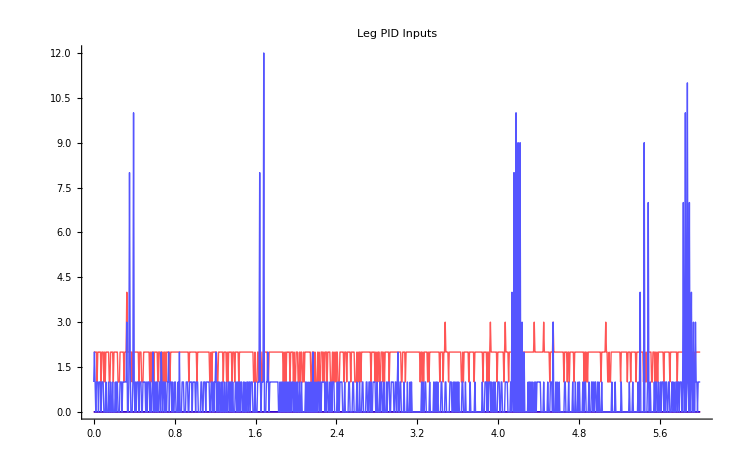

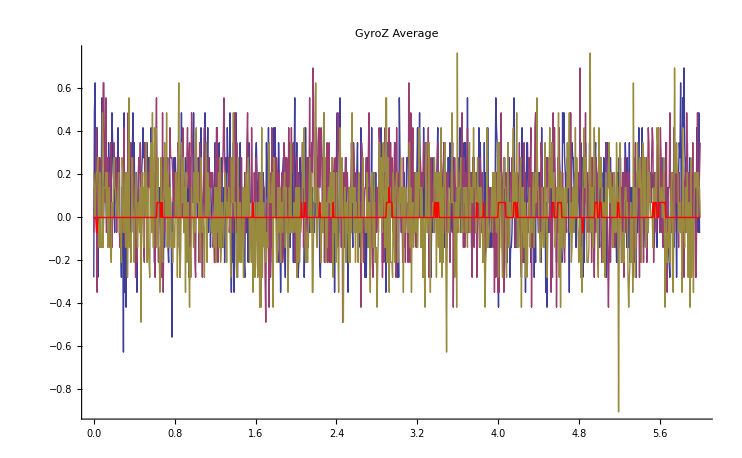

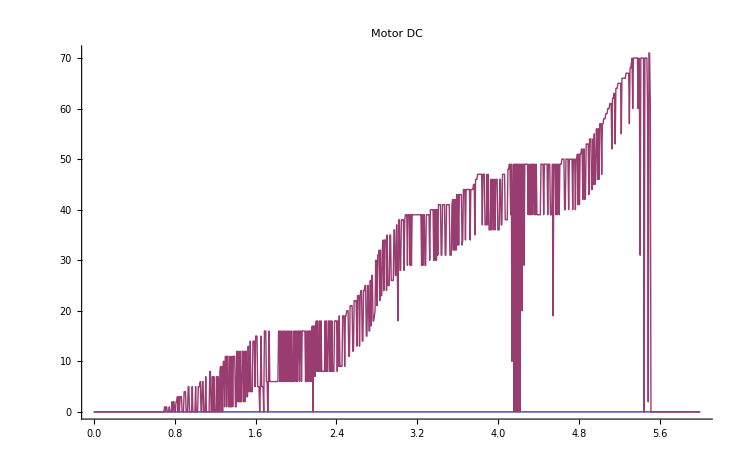

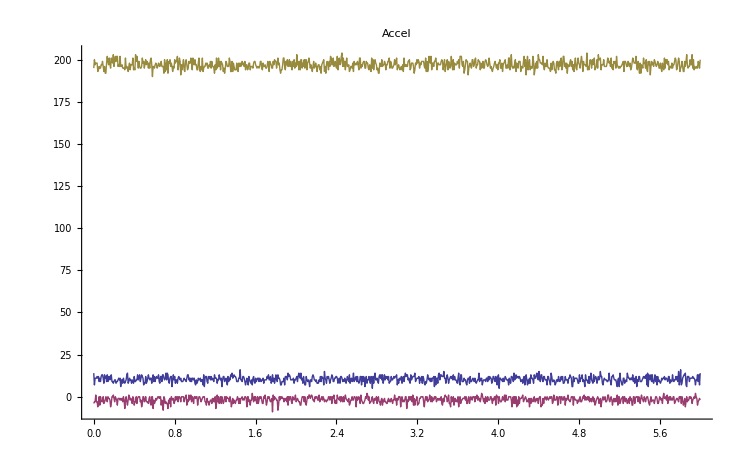

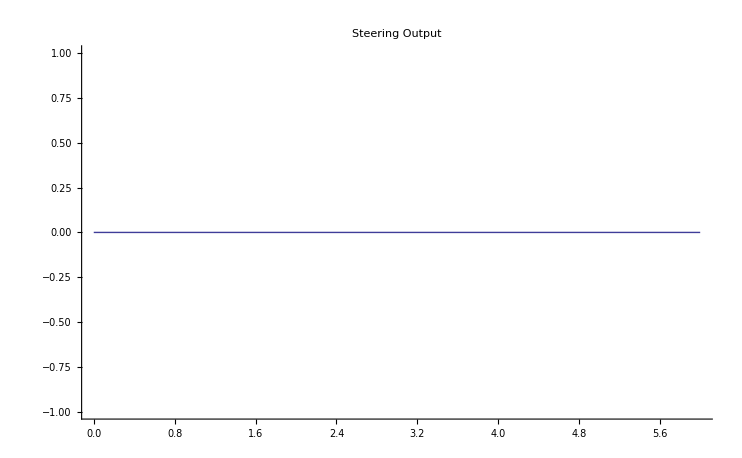

```mathematica
ListPlot[{{times,Llegs}ᵀ,{times,Rlegs}ᵀ,{times,LBEMF}ᵀ,{times,RBEMF}ᵀ},Joined->True,PlotRange->All,PlotLabel->"Leg PID Inputs",PlotStyle->{{Thick,Red},{Thick,Blue},{Thin,Lighter[Red]},{Thin,Lighter[Blue]}}]
ListPlot[{{times,GyroX}ᵀ,{times,GyroY}ᵀ,{times,GyroZ}ᵀ,{times,GyroZAvg}ᵀ},Joined->True,PlotRange->All,PlotLabel->"GyroZ Average",PlotStyle->{Automatic,Automatic,Automatic,{Thick,Red}}]
ListPlot[{{times,DCL}ᵀ,{times,DCR}ᵀ},Joined->True,PlotRange->All,PlotLabel->"Motor DC"]
ListPlot[{{times,AccelX}ᵀ,{times,AccelY}ᵀ,{times,AccelZ}ᵀ},Joined->True,PlotRange->All,PlotLabel->"Accel"]
ListPlot[{times,SteerOut}ᵀ,Joined->True,PlotRange->All,PlotLabel->"Steering Output"]
```

```mathematica
(****  Calculate integrated heading and do a linear fit ****)
```

0.990753

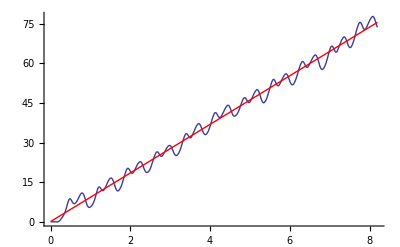

```mathematica
θz =Accumulate[Differences[times]*GyroZAvg[[;;-2]]];
lm=LinearModelFit[{times[[;;-2]],θz}ᵀ,x,x];
lm["RSquared"]
Show[ListPlot[{times[[;;-2]],θz}ᵀ, Joined->True, PlotStyle->Thick],
Plot[lm[x],{x,0,times[[-2]]},PlotStyle->Red] ]
```

```mathematica
(****   Frequency spectrum of Gyro   ****)
```

149.952

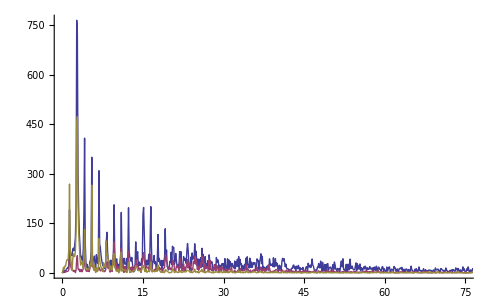

```mathematica
T = Mean[Differences[times]];
f = 1/T//N
Nn=Length[times];
F = Range[0,f,f/(Nn-1)];
Fx=Abs[Fourier[GyroX-Mean[GyroX]]];
Fy=Abs[Fourier[GyroY-Mean[GyroY]]];
Fz=Abs[Fourier[GyroZ-Mean[GyroZ]]];
ListPlot[{{F,Fx}ᵀ,{F,Fy}ᵀ,{F,Fz}ᵀ},Joined->True,PlotRange->{{0,f/2},All}]
```

```mathematica
(*** Checking telemtry timer accuracy and deviation ***)
1/(times[[2;;Length[times]]]-times[[1;;Length[times]-1]])//Mean//N
1/(times[[2;;Length[times]]]-times[[1;;Length[times]-1]])//StandardDeviation//N
```

149.956

0.734041

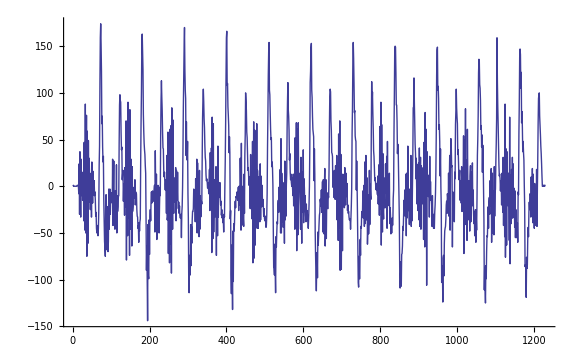

```mathematica
ListPlot[LBEMF-RBEMF,Joined->True]
```

```mathematica
Mean[LBEMF-RBEMF]//N
StandardDeviation[LBEMF-RBEMF]//N
```

0.397561

52.1141